### circuito 750 kV

```mathematica
r=.5/Cos[45. Degree]
```

0.707107

```mathematica
ns=4;
```

```mathematica
δx=Table[ r Cos[(n) 2 π/ns],{n,1,ns}];
δy=Table[ r Sin[(n) 2 π/ns],{n,1,ns}];
```

```mathematica
x=Flatten[{-15.8+δx, 0+δx,15.8+δx,-14.4,14.4}];
y=Flatten[{34.76+δy,35.26+δy,34.76+δy,41,41}];
```

```mathematica
xy1000kV=Thread[{x,y}]
```

{{-15.8,35.4671},{-16.5071,34.76},{-15.8,34.0529},{-15.0929,34.76},{0,35.9671},{-0.707107,35.26},{0,34.5529},{0.707107,35.26},{15.8,35.4671},{15.0929,34.76},{15.8,34.0529},{16.5071,34.76},{-14.4,41},{14.4,41}}

```mathematica
Dimensions[xy1000kV]
```

{14,2}

```mathematica
mostra1={Circle[#,.25]}&/@xy1000kV;
```

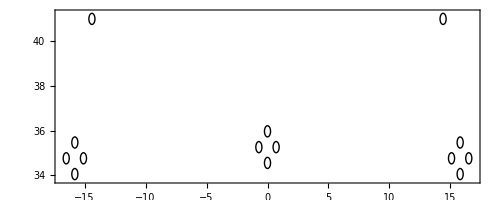

```mathematica
Show[Graphics[mostra1],Frame->True]
```